## The formulae

```mathematica
FindFullFormulaWithPrefix[g_,prefix_]:=Fold [Plus,Map[ChangeSymbol[#,prefix]&,FindFullFormula[g]]]
```

```mathematica
FindFullFormulaWithPrefix[CycleGraph[3],"A"]
```

A1x2x3

```mathematica
NextLetter[l_]:=FromCharacterCode[ToCharacterCode[l]+1]
```

```mathematica
NextLetter["D"]
```

E

```mathematica
CalculateInOutFormulaMany[g_,sets_, prefix_, verbose_:False]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex, in, out,inVertex,outVertex,
 contractSets},
If[verbose,Print[{"Task ","g",Graph[g,VertexLabels->"Name"],"sets",sets,"prefix", prefix , "node count", VertexCount[g]}]];
If[VertexCount[g]==0,
Print["VertexCount is zero",g,sets,prefix];
Return[1]
];
(* if there is no set, we have a problem *)
If[Length[sets]==0,
Print["No more sets"];
Interrupt[];
];
(* if there is only one set, we are done *)
If[Length[sets]==1,
result=FindFullFormulaWithPrefix[g,prefix];
Return[result];
];

(* there is more than 1 set : we define in to be the first set, out to be thejoin of the rest *)
in=First[sets];
out=Flatten[Rest[sets]];

(* the whole goal is to remove the  in *)
(* as long as there is an edge between in and out we remove and contract it and recurse *)
edges=EdgeList[g];
For[pos=1,pos <=Length[edges],pos++,
(* make sure currentEdge is of the form {in, out} *)
currentEdge=edges[[pos]];
isInOut=MemberQ[in,currentEdge[[1]]]&&MemberQ[out,currentEdge[[2]]];
If[!isInOut,
isInOut=MemberQ[in,currentEdge[[2]]]&&MemberQ[out,currentEdge[[1]]];
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
If[isInOut && (!MemberQ[in, currentEdge[[1]]]||!MemberQ[out,currentEdge[[2]]]),
Print["Problem"];
Interrupt[]
];
If[isInOut,
inVertex = currentEdge[[1]];
outVertex = currentEdge[[2]];
gContract=GContract[g,currentEdge];
repVertex={inVertex->outVertex}; (* replace the in by the out since we want ot get rid of the in *)
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
If[verbose,Print[{"gContract vertices",VertexList[gContract],"gContract edges",EdgeList[gContract]}]];
gRemove=EdgeDelete[g,currentEdge];
contractSets=Prepend[Rest[sets],DeleteCases[in,inVertex]];
If[verbose,Print[{currentEdge,"gContract",Graph[gContract,VertexLabels->"Name"],"gRemove",Graph[gRemove,VertexLabels->"Name"],"contractSets", contractSets}]];
If[verbose,Print["calculating resContract"]];
resContract=CalculateInOutFormulaMany[gContract,contractSets,prefix, verbose];
If[verbose,Print["calculating resRemove"]];
resRemove=CalculateInOutFormulaMany[gRemove,sets,prefix, verbose];
result=resRemove-resContract;
Return[result]
];
];

(* there are no more edges between in and out so we compute in and recurse with the rest *)
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
If[verbose,Print["All edges have been removed", "gIn", gIn, "gOut",gOut,"in", in, "out", out]];
resIn=If[VertexCount[gIn]==0,1,FindFullFormulaWithPrefix[gIn, prefix]];
resOut=If[VertexCount[gOut]==0,1,CalculateInOutFormulaMany[gOut,Rest[sets],NextLetter[prefix], verbose]];
Return[resIn*resOut]
]
```

```mathematica
CalculateInOutFormulaMany[g_,sets_,verbose_]:=CalculateInOutFormulaMany[g,Map[Sort,sets],"A", verbose]
```

```mathematica
CollectByPrefix[form_, prefixes_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],First[prefixes]]&], rest=Rest[prefixes], form2=form, term},
If[vars=={},
Factor[form],
Total[
Table[
Total[
With[{coeff=Last[CoefficientList[form2,v]]},
Table[
term=If[rest=={},
v^(k-1)*Factor[coeff[[k]]],
v^(k-1)*CollectByPrefix[Factor[coeff[[k]]],rest]
];
form2=form2-term;
term
,{k,Length[coeff]}]
]
],
{v,Select[vars,SymbolLevel[#]<=4&]}
]
]+form2
]
]
```

## Now some tests

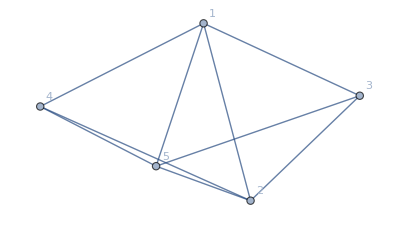

```mathematica
g=Graph[JacobsThalGraph[1],VertexLabels->"Name"]
```

```mathematica
CalculateInOutFormulaMany[g,{{1,2,5},{3},{4}}]
```

18 C4-24 B3 C4+2 A1 B3 C4-A1x2 B3 C4+A1x2x5 B3 C4-A1x5 B3 C4+2 A2 B3 C4-A2x5 B3 C4+2 A5 B3 C4+4 A1 (-C4+B3 C4)-A1x2 (-C4+B3 C4)-A1x5 (-C4+B3 C4)+4 A2 (-C4+B3 C4)-A2x5 (-C4+B3 C4)+4 A5 (-C4+B3 C4)

```mathematica
CollectByPrefix[A1*3+A1*x+B1,{"A"}]
```

B1+A1 (3+x)

```mathematica
CoefficientList[A1+B1,A1]
```

{B1,1}

```mathematica
CollectByPrefix[18 C4-24 B3 C4+2 A1 B3 C4-A1x2 B3 C4+A1x2x5 B3 C4-A1x5 B3 C4+2 A2 B3 C4-A2x5 B3 C4+2 A5 B3 C4+4 A1 (-C4+B3 C4)-A1x2 (-C4+B3 C4)-A1x5 (-C4+B3 C4)+4 A2 (-C4+B3 C4)-A2x5 (-C4+B3 C4)+4 A5 (-C4+B3 C4),{"A"}]
```

A1x2x5 B3 C4-A1x2 (-1+2 B3) C4-A1x5 (-1+2 B3) C4-A2x5 (-1+2 B3) C4+2 A1 (-2+3 B3) C4+2 A2 (-2+3 B3) C4+2 A5 (-2+3 B3) C4+(18-4 A1+A1x2+A1x5-4 A2+A2x5-24 B3+6 A1 B3-2 A1x2 B3+A1x2x5 B3-2 A1x5 B3+6 A2 B3-2 A2x5 B3) C4-(-18-A1x2-A1x5+4 A2-A2x5+4 A5+24 B3+2 A1x2 B3-A1x2x5 B3+2 A1x5 B3-6 A2 B3+2 A2x5 B3-6 A5 B3) C4+(18-4 A1+A1x2+A1x5-4 A2-4 A5-24 B3+6 A1 B3-2 A1x2 B3+A1x2x5 B3-2 A1x5 B3+6 A2 B3+6 A5 B3) C4+(18-4 A1+A1x2+A1x5+A2x5-4 A5-24 B3+6 A1 B3-2 A1x2 B3+A1x2x5 B3-2 A1x5 B3-2 A2x5 B3+6 A5 B3) C4+(18-4 A1+A1x2-4 A2+A2x5-4 A5-24 B3+6 A1 B3-2 A1x2 B3+A1x2x5 B3+6 A2 B3-2 A2x5 B3+6 A5 B3) C4+(18-4 A1+A1x2+A1x5-4 A2+A2x5-4 A5-24 B3+6 A1 B3-2 A1x2 B3-2 A1x5 B3+6 A2 B3-2 A2x5 B3+6 A5 B3) C4+(18-4 A1+A1x5-4 A2+A2x5-4 A5-24 B3+6 A1 B3+A1x2x5 B3-2 A1x5 B3+6 A2 B3-2 A2x5 B3+6 A5 B3) C4

## The simplest experiment

```mathematica
EdgeList[CycleGraph[3]]
```

{1<->2,1<->3,2<->3}

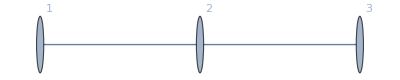

```mathematica
g=Graph[{1<->2,2<->3},VertexLabels->"Name"]
```

```mathematica
form=CalculateInOutFormulaMany[g,{{1},{2},{3}},False]
```

C3-B2 C3+A1 (-C3+B2 C3)

```mathematica
ChromaticPolynomial[g,x]
```

x-2 x^2+x^3

```mathematica
Expand[form/.{A1->x,B2->x,C3->x}]
```

x-2 x^2+x^3

```mathematica
Expand[form]
```

C3-A1 C3-B2 C3+A1 B2 C3

```mathematica
CollectByPrefix[form,{"A"}]
```

-(-1+B2) C3+A1 (-1+B2) C3

## Another experiment

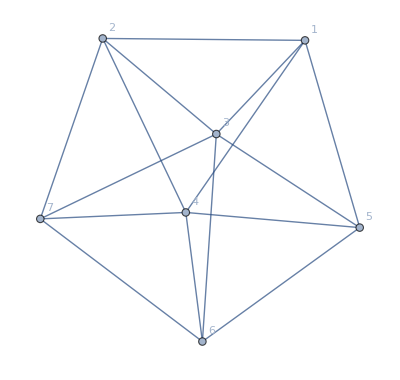

```mathematica
g=Graph[JacobsThalGraph[3],VertexLabels->"Name"]
```

```mathematica
form=CalculateInOutFormulaMany[g,{{1,2,7,6,5},{3},{4}},False]
```

210 C4-240 B3 C4+8 A1 B3 C4-4 A1x2 B3 C4+2 (A1x25+A1x2x5) B3 C4-(A16x25+A16x2x5+A1x25x6+A1x26x5+A1x2x5x6) B3 C4+(A16x25x7+A16x2x57+A16x2x5x7+A17x25x6+A17x26x5+A17x2x5x6+A1x25x6x7+A1x26x57+A1x26x5x7+A1x2x57x6+A1x2x5x6x7) B3 C4-(A17x25+A17x2x5+A1x25x7+A1x2x57+A1x2x5x7) B3 C4+(A16x2+A1x26+A1x2x6) B3 C4-(A16x2x7+A17x26+A17x2x6+A1x26x7+A1x2x6x7) B3 C4+2 (A17x2+A1x2x7) B3 C4-4 A1x5 B3 C4+2 (A16x5+A1x5x6) B3 C4-(A16x57+A16x5x7+A17x5x6+A1x57x6+A1x5x6x7) B3 C4+(A17x5+A1x57+A1x5x7) B3 C4-2 (A16+A1x6) B3 C4+(A16x7+A17x6+A1x6x7) B3 C4-2 (A17+A1x7) B3 C4+8 A2 B3 C4-2 (A25+A2x5) B3 C4+(A25x6+A26x5+A2x5x6) B3 C4-(A25x6x7+A26x57+A26x5x7+A2x57x6+A2x5x6x7) B3 C4+(A25x7+A2x57+A2x5x7) B3 C4-2 (A26+A2x6) B3 C4+2 (A26x7+A2x6x7) B3 C4-4 A2x7 B3 C4+8 A5 B3 C4-4 A5x6 B3 C4+2 (A57x6+A5x6x7) B3 C4-2 (A57+A5x7) B3 C4+8 A6 B3 C4-4 A6x7 B3 C4+8 A7 B3 C4+46 A1 (-C4+B3 C4)-14 A1x2 (-C4+B3 C4)+4 (A1x25+A1x2x5) (-C4+B3 C4)-(A16x25+A16x2x5+A1x25x6+A1x26x5+A1x2x5x6) (-C4+B3 C4)-(A17x25+A17x2x5+A1x25x7+A1x2x57+A1x2x5x7) (-C4+B3 C4)+3 (A16x2+A1x26+A1x2x6) (-C4+B3 C4)-(A16x2x7+A17x26+A17x2x6+A1x26x7+A1x2x6x7) (-C4+B3 C4)+4 (A17x2+A1x2x7) (-C4+B3 C4)-14 A1x5 (-C4+B3 C4)+4 (A16x5+A1x5x6) (-C4+B3 C4)-(A16x57+A16x5x7+A17x5x6+A1x57x6+A1x5x6x7) (-C4+B3 C4)+3 (A17x5+A1x57+A1x5x7) (-C4+B3 C4)-10 (A16+A1x6) (-C4+B3 C4)+3 (A16x7+A17x6+A1x6x7) (-C4+B3 C4)-10 (A17+A1x7) (-C4+B3 C4)+46 A2 (-C4+B3 C4)-10 (A25+A2x5) (-C4+B3 C4)+3 (A25x6+A26x5+A2x5x6) (-C4+B3 C4)-(A25x6x7+A26x57+A26x5x7+A2x57x6+A2x5x6x7) (-C4+B3 C4)+3 (A25x7+A2x57+A2x5x7) (-C4+B3 C4)-10 (A26+A2x6) (-C4+B3 C4)+4 (A26x7+A2x6x7) (-C4+B3 C4)-14 A2x7 (-C4+B3 C4)+46 A5 (-C4+B3 C4)-14 A5x6 (-C4+B3 C4)+4 (A57x6+A5x6x7) (-C4+B3 C4)-10 (A57+A5x7) (-C4+B3 C4)+46 A6 (-C4+B3 C4)-14 A6x7 (-C4+B3 C4)+46 A7 (-C4+B3 C4)

```mathematica
form=CalculateInOutFormulaMany[g,{{3},{1,2,7,6,5},{4}},False]
```

210 C4-54 B1 C4+22 B1x2 C4-2 B1x2x5 C4-8 (B1x25+B1x2x5) C4+(B16x2x5+B1x2x5x6) C4+(B1x25x6+B1x26x5+B1x2x5x6) C4+3 (B16x25+B16x2x5+B1x25x6+B1x26x5+B1x2x5x6) C4-(B16x25x7+B16x2x5x7+B17x25x6+B17x26x5+B17x2x5x6+B1x25x6x7+B1x26x5x7+B1x2x5x6x7) C4-(B16x2x57+B16x2x5x7+B17x2x5x6+B1x2x57x6+B1x2x5x6x7) C4-(B1x25x6x7+B1x26x57+B1x26x5x7+B1x2x57x6+B1x2x5x6x7) C4-2 (B16x25x7+B16x2x57+B16x2x5x7+B17x25x6+B17x26x5+B17x2x5x6+B1x25x6x7+B1x26x57+B1x26x5x7+B1x2x57x6+B1x2x5x6x7) C4+(B17x25+B17x2x5+B1x25x7+B1x2x5x7) C4+(B17x2x5+B1x2x57+B1x2x5x7) C4+(B1x25x7+B1x2x57+B1x2x5x7) C4+2 (B17x25+B17x2x5+B1x25x7+B1x2x57+B1x2x5x7) C4-(B16x2+B1x2x6) C4-(B1x26+B1x2x6) C4-4 (B16x2+B1x26+B1x2x6) C4+(B16x2x7+B17x2x6+B1x2x6x7) C4+(B1x26x7+B1x2x6x7) C4+3 (B16x2x7+B17x26+B17x2x6+B1x26x7+B1x2x6x7) C4-2 B1x2x7 C4-8 (B17x2+B1x2x7) C4+22 B1x5 C4-2 B1x5x6 C4-8 (B16x5+B1x5x6) C4+(B16x5x7+B17x5x6+B1x5x6x7) C4+(B1x57x6+B1x5x6x7) C4+3 (B16x57+B16x5x7+B17x5x6+B1x57x6+B1x5x6x7) C4-(B17x5+B1x5x7) C4-(B1x57+B1x5x7) C4-4 (B17x5+B1x57+B1x5x7) C4+2 B1x6 C4+12 (B16+B1x6) C4-B1x6x7 C4-5 (B16x7+B17x6+B1x6x7) C4+2 B1x7 C4+12 (B17+B1x7) C4-54 B2 C4+2 B2x5 C4+12 (B25+B2x5) C4-B2x5x6 C4-5 (B25x6+B26x5+B2x5x6) C4+(B25x6x7+B26x5x7+B2x5x6x7) C4+(B2x57x6+B2x5x6x7) C4+3 (B25x6x7+B26x57+B26x5x7+B2x57x6+B2x5x6x7) C4-(B25x7+B2x5x7) C4-(B2x57+B2x5x7) C4-4 (B25x7+B2x57+B2x5x7) C4+2 B2x6 C4+12 (B26+B2x6) C4-2 B2x6x7 C4-8 (B26x7+B2x6x7) C4+22 B2x7 C4-54 B5 C4+22 B5x6 C4-2 B5x6x7 C4-8 (B57x6+B5x6x7) C4+2 B5x7 C4+12 (B57+B5x7) C4-54 B6 C4+22 B6x7 C4-54 B7 C4+A3 (-30 C4+8 B1 C4-4 B1x2 C4+2 (B1x25+B1x2x5) C4-(B16x25+B16x2x5+B1x25x6+B1x26x5+B1x2x5x6) C4+(B16x25x7+B16x2x57+B16x2x5x7+B17x25x6+B17x26x5+B17x2x5x6+B1x25x6x7+B1x26x57+B1x26x5x7+B1x2x57x6+B1x2x5x6x7) C4-(B17x25+B17x2x5+B1x25x7+B1x2x57+B1x2x5x7) C4+(B16x2+B1x26+B1x2x6) C4-(B16x2x7+B17x26+B17x2x6+B1x26x7+B1x2x6x7) C4+2 (B17x2+B1x2x7) C4-4 B1x5 C4+2 (B16x5+B1x5x6) C4-(B16x57+B16x5x7+B17x5x6+B1x57x6+B1x5x6x7) C4+(B17x5+B1x57+B1x5x7) C4-2 (B16+B1x6) C4+(B16x7+B17x6+B1x6x7) C4-2 (B17+B1x7) C4+8 B2 C4-2 (B25+B2x5) C4+(B25x6+B26x5+B2x5x6) C4-(B25x6x7+B26x57+B26x5x7+B2x57x6+B2x5x6x7) C4+(B25x7+B2x57+B2x5x7) C4-2 (B26+B2x6) C4+2 (B26x7+B2x6x7) C4-4 B2x7 C4+8 B5 C4-4 B5x6 C4+2 (B57x6+B5x6x7) C4-2 (B57+B5x7) C4+8 B6 C4-4 B6x7 C4+8 B7 C4)

```mathematica
form3=CalculateInOutFormulaMany[g,{{3},{4},{1,2,7,6,5}},False]
```

9 C16x25x7+9 C16x2x57+16 C16x2x5x7+9 C17x25x6+9 C17x26x5+16 C17x2x5x6+16 C1x25x6x7+9 C1x26x57+16 C1x26x5x7+16 C1x2x57x6+25 C1x2x5x6x7-B4 (C16x25x7+C16x2x5x7+C17x25x6+C17x26x5+C17x2x5x6+C1x25x6x7+C1x26x5x7+C1x2x5x6x7)-B4 (C16x2x57+C16x2x5x7+C17x2x5x6+C1x2x57x6+C1x2x5x6x7)-B4 (C1x25x6x7+C1x26x57+C1x26x5x7+C1x2x57x6+C1x2x5x6x7)-2 B4 (C16x25x7+C16x2x57+C16x2x5x7+C17x25x6+C17x26x5+C17x2x5x6+C1x25x6x7+C1x26x57+C1x26x5x7+C1x2x57x6+C1x2x5x6x7)+A3 (-3 C16x25x7-3 C16x2x57-4 C16x2x5x7-3 C17x25x6-3 C17x26x5-4 C17x2x5x6-4 C1x25x6x7-3 C1x26x57-4 C1x26x5x7-4 C1x2x57x6-5 C1x2x5x6x7+B4 (C16x25x7+C16x2x57+C16x2x5x7+C17x25x6+C17x26x5+C17x2x5x6+C1x25x6x7+C1x26x57+C1x26x5x7+C1x2x57x6+C1x2x5x6x7))

```mathematica
CollectByPrefix[form3,{"C"}]
```

81 C16x25x7-27 A3 C16x25x7+(-3+A3) (-3+B4) C16x25x7-27 B4 C16x25x7+9 A3 B4 C16x25x7+81 C16x2x57-27 A3 C16x2x57+(-3+A3) (-3+B4) C16x2x57-27 B4 C16x2x57+9 A3 B4 C16x2x57+144 C16x2x5x7-36 A3 C16x2x5x7+(-4+A3) (-4+B4) C16x2x5x7-36 B4 C16x2x5x7+9 A3 B4 C16x2x5x7+81 C17x25x6-27 A3 C17x25x6+(-3+A3) (-3+B4) C17x25x6-27 B4 C17x25x6+9 A3 B4 C17x25x6+81 C17x26x5-27 A3 C17x26x5+(-3+A3) (-3+B4) C17x26x5-27 B4 C17x26x5+9 A3 B4 C17x26x5+144 C17x2x5x6-36 A3 C17x2x5x6+(-4+A3) (-4+B4) C17x2x5x6-36 B4 C17x2x5x6+9 A3 B4 C17x2x5x6+144 C1x25x6x7-36 A3 C1x25x6x7+(-4+A3) (-4+B4) C1x25x6x7-36 B4 C1x25x6x7+9 A3 B4 C1x25x6x7+81 C1x26x57-27 A3 C1x26x57+(-3+A3) (-3+B4) C1x26x57-27 B4 C1x26x57+9 A3 B4 C1x26x57+144 C1x26x5x7-36 A3 C1x26x5x7+(-4+A3) (-4+B4) C1x26x5x7-36 B4 C1x26x5x7+9 A3 B4 C1x26x5x7+144 C1x2x57x6-36 A3 C1x2x57x6+(-4+A3) (-4+B4) C1x2x57x6-36 B4 C1x2x57x6+9 A3 B4 C1x2x57x6+250 C1x2x5x6x7-50 A3 C1x2x5x6x7-50 B4 C1x2x5x6x7+10 A3 B4 C1x2x5x6x7

```mathematica
form4=CalculateInOutFormulaMany[g,{{3},{1,2,7,6,5,4}},False]
```

-3 B16x25x4x7-3 B16x2x4x57-4 B16x2x4x5x7-3 B17x25x4x6-3 B17x26x4x5-4 B17x2x4x5x6-4 B1x25x4x6x7-3 B1x26x4x57-4 B1x26x4x5x7-4 B1x2x4x57x6-5 B1x2x4x5x6x7+A3 (B16x25x4x7+B16x2x4x57+B16x2x4x5x7+B17x25x4x6+B17x26x4x5+B17x2x4x5x6+B1x25x4x6x7+B1x26x4x57+B1x26x4x5x7+B1x2x4x57x6+B1x2x4x5x6x7)

```mathematica
MyRewrite[form_,prefix_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],prefix]&],form2=form},
Print[vars];
If[vars=={},
Factor[form],
Total[
Table[
v*Factor[Last[CoefficientList[form,v]]],
{v,vars}
]
]
]
]
```

```mathematica
MyRewrite2[form_,prefix_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],prefix]&],form2=form, term},
Print[vars];
If[vars=={},
Factor[form],
Total[
Table[
term=v*Factor[Last[CoefficientList[form2,v]]];
form2=Simplify[form2-term];
term
,
{v,vars}
]
]+form2
]
]
```

```mathematica
MyRewrite2[form_, prefixes_]:=Block[{vars,form2=form, term, rest}, 
If[prefixes=={},Return[form]];
vars=DeleteDuplicates[ListofVars[form]];
vars=Select[vars,StringStartsQ[ SymbolName[#],First[prefixes]]&];
rest=Rest[prefixes];
If[vars=={},
Factor[form],
Total[
Table[
term=v*MyRewrite2[Factor[Last[CoefficientList[form2,v]]],rest];
form2=Simplify[form2-term];
term
,
{v,vars}
]
]+form2
]
]
```

```mathematica
MyRewrite[form4,"B"]
```

{B16x25x4x7,B16x2x4x57,B16x2x4x5x7,B17x25x4x6,B17x26x4x5,B17x2x4x5x6,B1x25x4x6x7,B1x26x4x57,B1x26x4x5x7,B1x2x4x57x6,B1x2x4x5x6x7}

(-3+A3) B16x25x4x7+(-3+A3) B16x2x4x57+(-4+A3) B16x2x4x5x7+(-3+A3) B17x25x4x6+(-3+A3) B17x26x4x5+(-4+A3) B17x2x4x5x6+(-4+A3) B1x25x4x6x7+(-3+A3) B1x26x4x57+(-4+A3) B1x26x4x5x7+(-4+A3) B1x2x4x57x6+(-5+A3) B1x2x4x5x6x7

```mathematica
MyRewrite2[form4,"B"]
```

{B16x25x4x7,B16x2x4x57,B16x2x4x5x7,B17x25x4x6,B17x26x4x5,B17x2x4x5x6,B1x25x4x6x7,B1x26x4x57,B1x26x4x5x7,B1x2x4x57x6,B1x2x4x5x6x7}

(-3+A3) B16x25x4x7+(-3+A3) B16x2x4x57+(-4+A3) B16x2x4x5x7+(-3+A3) B17x25x4x6+(-3+A3) B17x26x4x5+(-4+A3) B17x2x4x5x6+(-4+A3) B1x25x4x6x7+(-3+A3) B1x26x4x57+(-4+A3) B1x26x4x5x7+(-4+A3) B1x2x4x57x6+(-5+A3) B1x2x4x5x6x7

```mathematica
MyRewrite2[form3,{"C","B","A"}]
```

(9-3 A3+(-3+A3) B4) C16x25x7+(9-3 A3+(-3+A3) B4) C16x2x57+(-4 (-4+A3)+(-4+A3) B4) C16x2x5x7+(9-3 A3+(-3+A3) B4) C17x25x6+(9-3 A3+(-3+A3) B4) C17x26x5+(-4 (-4+A3)+(-4+A3) B4) C17x2x5x6+(-4 (-4+A3)+(-4+A3) B4) C1x25x6x7+(9-3 A3+(-3+A3) B4) C1x26x57+(-4 (-4+A3)+(-4+A3) B4) C1x26x5x7+(-4 (-4+A3)+(-4+A3) B4) C1x2x57x6+(-5 (-5+A3)+(-5+A3) B4) C1x2x5x6x7

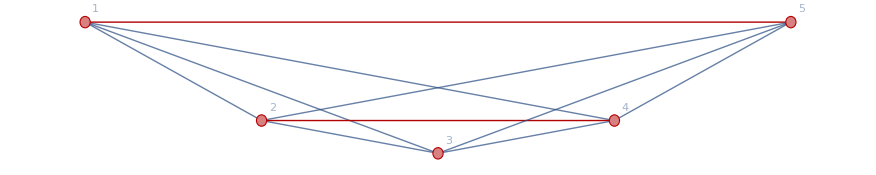

```mathematica
GraphFromSymbol[C15x24x3]
```

```mathematica
SymbolToGraph[s_]:=Block[{sets=SymbolToSets[s],result, labels},
labels=Table[k->Rotate[Row[sets[[k]], ","],-Pi/6],{k,Length[sets]}];
CompleteGraph[Length[sets],VertexLabels->labels,GraphLayout->"TutteEmbedding", ImageSize->70, VertexStyle->Red, VertexSize->0.1, EdgeStyle->Darker[Green]]
]
```

```mathematica
SymbolToGraph[C16x25x7]
```

-Graphics-

```mathematica
MyRewrite2[form3,{"C"}]/.{B4->x,A3->x}
```

C1x2x5x6x7 (-5+x)^2+C16x2x5x7 (-4+x)^2+C17x2x5x6 (-4+x)^2+C1x25x6x7 (-4+x)^2+C1x26x5x7 (-4+x)^2+C1x2x57x6 (-4+x)^2+C16x25x7 (-3+x)^2+C16x2x57 (-3+x)^2+C17x25x6 (-3+x)^2+C17x26x5 (-3+x)^2+C1x26x57 (-3+x)^2

```mathematica
Map[SymbolToGraph,MyRewrite2[form3,{"C"}]/.{B4->x,A3->x}/.x->4]
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+

```mathematica
MyRewrite2[form4,{"B"}]
```

(-3+A3) B16x25x4x7+(-3+A3) B16x2x4x57+(-4+A3) B16x2x4x5x7+(-3+A3) B17x25x4x6+(-3+A3) B17x26x4x5+(-4+A3) B17x2x4x5x6+(-4+A3) B1x25x4x6x7+(-3+A3) B1x26x4x57+(-4+A3) B1x26x4x5x7+(-4+A3) B1x2x4x57x6+(-5+A3) B1x2x4x5x6x7

```mathematica
Map[SymbolToGraph,MyRewrite2[form4,{"C"}]/.{B4->x,A3->x}/.x->4]
```

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
CoefficientList[Expand[form3],A3]
```

{9 C16x25x7-3 B4 C16x25x7+9 C16x2x57-3 B4 C16x2x57+16 C16x2x5x7-4 B4 C16x2x5x7+9 C17x25x6-3 B4 C17x25x6+9 C17x26x5-3 B4 C17x26x5+16 C17x2x5x6-4 B4 C17x2x5x6+16 C1x25x6x7-4 B4 C1x25x6x7+9 C1x26x57-3 B4 C1x26x57+16 C1x26x5x7-4 B4 C1x26x5x7+16 C1x2x57x6-4 B4 C1x2x57x6+25 C1x2x5x6x7-5 B4 C1x2x5x6x7,-3 C16x25x7+B4 C16x25x7-3 C16x2x57+B4 C16x2x57-4 C16x2x5x7+B4 C16x2x5x7-3 C17x25x6+B4 C17x25x6-3 C17x26x5+B4 C17x26x5-4 C17x2x5x6+B4 C17x2x5x6-4 C1x25x6x7+B4 C1x25x6x7-3 C1x26x57+B4 C1x26x57-4 C1x26x5x7+B4 C1x26x5x7-4 C1x2x57x6+B4 C1x2x57x6-5 C1x2x5x6x7+B4 C1x2x5x6x7}

```mathematica
MyRewrite[form3,"C"]
```

(-3+A3) (-3+B4) C16x25x7+(-3+A3) (-3+B4) C16x2x57+(-4+A3) (-4+B4) C16x2x5x7+(-3+A3) (-3+B4) C17x25x6+(-3+A3) (-3+B4) C17x26x5+(-4+A3) (-4+B4) C17x2x5x6+(-4+A3) (-4+B4) C1x25x6x7+(-3+A3) (-3+B4) C1x26x57+(-4+A3) (-4+B4) C1x26x5x7+(-4+A3) (-4+B4) C1x2x57x6+(-5+A3) (-5+B4) C1x2x5x6x7

```mathematica
A3,
```

```mathematica
CollectByPrefix[form,{"A"}]
```

A16x25x7 B3 C4+A16x2x57 B3 C4+197+1+(210-46 A1-3 A16x2+A16x25+A16x2x5+A16x2x7-4 A16x5+A16x57+A16x5x7-3 A16x7+10 A17-4 A17x2+A17x25+A17x26+A17x2x5+A17x2x6-3 A17x5+A17x5x6-3 A17x6+14 A1x2-4 A1x25+A1x25x6+A1x25x7-3 A1x26+A1x26x5+A1x26x7-4 A1x2x5+A1x2x57+A1x2x5x6+A1x2x5x7-3 A1x2x6+A1x2x6x7-4 A1x2x7+14 A1x5-3 A1x57+119+4 A1x57 B3-2 A1x57x6 B3+6 A1x5x6 B3-2 A1x5x6x7 B3+4 A1x5x7 B3-12 A1x6 B3+4 A1x6x7 B3-12 A1x7 B3+54 A2 B3-12 A25 B3+4 A25x6 B3-2 A25x6x7 B3+4 A25x7 B3-12 A26 B3+4 A26x5 B3-2 A26x57 B3-2 A26x5x7 B3+6 A26x7 B3-12 A2x5 B3+4 A2x57 B3-2 A2x57x6 B3+4 A2x5x6 B3-2 A2x5x6x7 B3+4 A2x5x7 B3-12 A2x6 B3+6 A2x6x7 B3-18 A2x7 B3+54 A5 B3-12 A57 B3+6 A57x6 B3-18 A5x6 B3+6 A5x6x7 B3-12 A5x7 B3+54 A6 B3-18 A6x7 B3+54 A7 B3) C4
 |  |  |  |

```mathematica
form=CalculateInOutFormulaMany[g,{{1,2,7,6,5},{3},{4}},"X"]
```

210 Z4-240 Y3 Z4+8 X1 Y3 Z4-4 X1x2 Y3 Z4+2 (X1x25+X1x2x5) Y3 Z4-(X16x25+X16x2x5+X1x25x6+X1x26x5+X1x2x5x6) Y3 Z4+(X16x25x7+X16x2x57+X16x2x5x7+X17x25x6+X17x26x5+X17x2x5x6+X1x25x6x7+X1x26x57+X1x26x5x7+X1x2x57x6+X1x2x5x6x7) Y3 Z4-(X17x25+X17x2x5+X1x25x7+X1x2x57+X1x2x5x7) Y3 Z4+(X16x2+X1x26+X1x2x6) Y3 Z4-(X16x2x7+X17x26+X17x2x6+X1x26x7+X1x2x6x7) Y3 Z4+2 (X17x2+X1x2x7) Y3 Z4-4 X1x5 Y3 Z4+2 (X16x5+X1x5x6) Y3 Z4-(X16x57+X16x5x7+X17x5x6+X1x57x6+X1x5x6x7) Y3 Z4+(X17x5+X1x57+X1x5x7) Y3 Z4-2 (X16+X1x6) Y3 Z4+(X16x7+X17x6+X1x6x7) Y3 Z4-2 (X17+X1x7) Y3 Z4+8 X2 Y3 Z4-2 (X25+X2x5) Y3 Z4+(X25x6+X26x5+X2x5x6) Y3 Z4-(X25x6x7+X26x57+X26x5x7+X2x57x6+X2x5x6x7) Y3 Z4+(X25x7+X2x57+X2x5x7) Y3 Z4-2 (X26+X2x6) Y3 Z4+2 (X26x7+X2x6x7) Y3 Z4-4 X2x7 Y3 Z4+8 X5 Y3 Z4-4 X5x6 Y3 Z4+2 (X57x6+X5x6x7) Y3 Z4-2 (X57+X5x7) Y3 Z4+8 X6 Y3 Z4-4 X6x7 Y3 Z4+8 X7 Y3 Z4+46 X1 (-Z4+Y3 Z4)-14 X1x2 (-Z4+Y3 Z4)+4 (X1x25+X1x2x5) (-Z4+Y3 Z4)-(X16x25+X16x2x5+X1x25x6+X1x26x5+X1x2x5x6) (-Z4+Y3 Z4)-(X17x25+X17x2x5+X1x25x7+X1x2x57+X1x2x5x7) (-Z4+Y3 Z4)+3 (X16x2+X1x26+X1x2x6) (-Z4+Y3 Z4)-(X16x2x7+X17x26+X17x2x6+X1x26x7+X1x2x6x7) (-Z4+Y3 Z4)+4 (X17x2+X1x2x7) (-Z4+Y3 Z4)-14 X1x5 (-Z4+Y3 Z4)+4 (X16x5+X1x5x6) (-Z4+Y3 Z4)-(X16x57+X16x5x7+X17x5x6+X1x57x6+X1x5x6x7) (-Z4+Y3 Z4)+3 (X17x5+X1x57+X1x5x7) (-Z4+Y3 Z4)-10 (X16+X1x6) (-Z4+Y3 Z4)+3 (X16x7+X17x6+X1x6x7) (-Z4+Y3 Z4)-10 (X17+X1x7) (-Z4+Y3 Z4)+46 X2 (-Z4+Y3 Z4)-10 (X25+X2x5) (-Z4+Y3 Z4)+3 (X25x6+X26x5+X2x5x6) (-Z4+Y3 Z4)-(X25x6x7+X26x57+X26x5x7+X2x57x6+X2x5x6x7) (-Z4+Y3 Z4)+3 (X25x7+X2x57+X2x5x7) (-Z4+Y3 Z4)-10 (X26+X2x6) (-Z4+Y3 Z4)+4 (X26x7+X2x6x7) (-Z4+Y3 Z4)-14 X2x7 (-Z4+Y3 Z4)+46 X5 (-Z4+Y3 Z4)-14 X5x6 (-Z4+Y3 Z4)+4 (X57x6+X5x6x7) (-Z4+Y3 Z4)-10 (X57+X5x7) (-Z4+Y3 Z4)+46 X6 (-Z4+Y3 Z4)-14 X6x7 (-Z4+Y3 Z4)+46 X7 (-Z4+Y3 Z4)

```mathematica
DeleteDuplicates[ListofVars[form]]
```

{Z4,Y3,X1,X1x2,X1x5,X2,X2x7,X5,X5x6,X6,X6x7,X7,X16,X1x6,X16x5,X1x5x6,X17,X1x7,X17x2,X1x2x7,X1x25,X1x2x5,X25,X2x5,X26,X2x6,X26x7,X2x6x7,X57,X5x7,X57x6,X5x6x7,X16x2,X1x26,X1x2x6,X16x7,X17x6,X1x6x7,X17x5,X1x57,X1x5x7,X25x6,X26x5,X2x5x6,X25x7,X2x57,X2x5x7,X16x25,X16x2x5,X1x25x6,X1x26x5,X1x2x5x6,X16x2x7,X17x26,X17x2x6,X1x26x7,X1x2x6x7,X16x57,X16x5x7,X17x5x6,X1x57x6,X1x5x6x7,X17x25,X17x2x5,X1x25x7,X1x2x57,X1x2x5x7,X25x6x7,X26x57,X26x5x7,X2x57x6,X2x5x6x7,X16x25x7,X16x2x57,X16x2x5x7,X17x25x6,X17x26x5,X17x2x5x6,X1x25x6x7,X1x26x57,X1x26x5x7,X1x2x57x6,X1x2x5x6x7}

```mathematica
CollectByPrefix[form,{"X"}]
```

X16x25x7 Y3 Z4+X16x2x57 Y3 Z4+197+1+(210-46 X1-3 X16x2+X16x25+X16x2x5+X16x2x7-4 X16x5+X16x57+X16x5x7-3 X16x7+10 X17-4 X17x2+X17x25+X17x26+X17x2x5+X17x2x6-3 X17x5+X17x5x6-3 X17x6+14 X1x2-4 X1x25+X1x25x6+X1x25x7-3 X1x26+X1x26x5+X1x26x7-4 X1x2x5+X1x2x57+X1x2x5x6+X1x2x5x7-3 X1x2x6+X1x2x6x7-4 X1x2x7+14 X1x5-3 X1x57+119+4 X1x57 Y3-2 X1x57x6 Y3+6 X1x5x6 Y3-2 X1x5x6x7 Y3+4 X1x5x7 Y3-12 X1x6 Y3+4 X1x6x7 Y3-12 X1x7 Y3+54 X2 Y3-12 X25 Y3+4 X25x6 Y3-2 X25x6x7 Y3+4 X25x7 Y3-12 X26 Y3+4 X26x5 Y3-2 X26x57 Y3-2 X26x5x7 Y3+6 X26x7 Y3-12 X2x5 Y3+4 X2x57 Y3-2 X2x57x6 Y3+4 X2x5x6 Y3-2 X2x5x6x7 Y3+4 X2x5x7 Y3-12 X2x6 Y3+6 X2x6x7 Y3-18 X2x7 Y3+54 X5 Y3-12 X57 Y3+6 X57x6 Y3-18 X5x6 Y3+6 X5x6x7 Y3-12 X5x7 Y3+54 X6 Y3-18 X6x7 Y3+54 X7 Y3) Z4
 |  |  |  |

```mathematica
CollectByPrefix[CalculateInOutFormulaMany[g,{{1,2,7,6,5},{3},{4}}],{"A"}]
```

## Next jacobsthal

## Another experiment

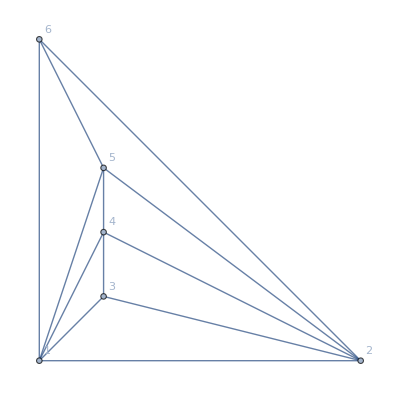

```mathematica
g=Graph[MinimalGraph[5],VertexLabels->"Name"]
```

```mathematica
form=CalculateInOutFormulaMany[g,{{1,2,4,6},{3},{5}},False]
```

-54 C5+72 B3 C5-4 A1 B3 C5+A1x2 B3 C5-A1x2x4 B3 C5+(A1x2x46+A1x2x4x6) B3 C5-A1x2x6 B3 C5+2 A1x4 B3 C5-(A1x46+A1x4x6) B3 C5+2 A1x6 B3 C5-4 A2 B3 C5+2 A2x4 B3 C5-(A2x46+A2x4x6) B3 C5+2 A2x6 B3 C5-6 A4 B3 C5+2 (A46+A4x6) B3 C5-6 A6 B3 C5-8 A1 (-C5+B3 C5)+A1x2 (-C5+B3 C5)-A1x2x6 (-C5+B3 C5)+2 A1x4 (-C5+B3 C5)-(A1x46+A1x4x6) (-C5+B3 C5)+4 A1x6 (-C5+B3 C5)-8 A2 (-C5+B3 C5)+2 A2x4 (-C5+B3 C5)-(A2x46+A2x4x6) (-C5+B3 C5)+4 A2x6 (-C5+B3 C5)-12 A4 (-C5+B3 C5)+4 (A46+A4x6) (-C5+B3 C5)-18 A6 (-C5+B3 C5)

```mathematica
form2=CalculateInOutFormulaMany[g,{{3},{5},{1,2,4,6}},False]
```

9 C1x2x46+12 C1x2x4x6-3 B5 (C1x2x46+C1x2x4x6)+A3 (-3 C1x2x46-4 C1x2x4x6+B5 (C1x2x46+C1x2x4x6))

```mathematica
MyRewrite2[form2,{"C"}]
```

(-3+A3) (-3+B5) C1x2x46+(-3+A3) (-4+B5) C1x2x4x6

```mathematica
MyRewrite2[form,{"A"}]
```

-A1x2x4 B3 C5+A1x2x46 B3 C5+A1x2x4x6 B3 C5+A1x2 (-1+2 B3) C5-A1x2x6 (-1+2 B3) C5+2 A1x4 (-1+2 B3) C5-A1x46 (-1+2 B3) C5-A1x4x6 (-1+2 B3) C5+2 A2x4 (-1+2 B3) C5-A2x46 (-1+2 B3) C5-A2x4x6 (-1+2 B3) C5-4 A1 (-2+3 B3) C5+2 A1x6 (-2+3 B3) C5-4 A2 (-2+3 B3) C5+2 A2x6 (-2+3 B3) C5-6 A4 (-2+3 B3) C5+2 A46 (-2+3 B3) C5+2 A4x6 (-2+3 B3) C5+18 (-3+4 B3) C5-6 A6 (-3+4 B3) C5

```mathematica
MyRewrite2[form,{"A"}]==form//Simplify
```

True

## Another experiment

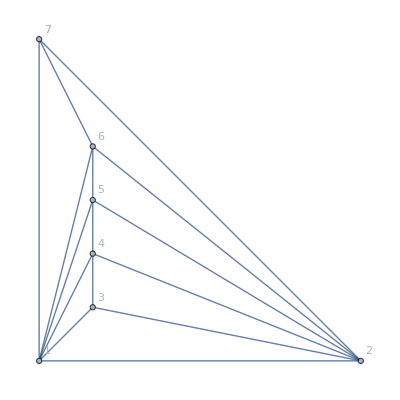

```mathematica
g=Graph[MinimalGraph[6],VertexLabels->"Name"]
```

```mathematica
form=CalculateInOutFormulaMany[g,{{1,2,4,6},{3},{5,7}},False]
```

-54 C57-216 C5x7+120 B3 C5x7-8 A1 B3 C5x7+A1x2 B3 C5x7-A1x2x4 B3 C5x7+4 A1x4 B3 C5x7-(A1x46+A1x4x6) B3 C5x7+2 A1x6 B3 C5x7-8 A2 B3 C5x7+4 A2x4 B3 C5x7-(A2x46+A2x4x6) B3 C5x7+2 A2x6 B3 C5x7-18 A4 B3 C5x7+4 (A46+A4x6) B3 C5x7-12 A6 B3 C5x7+72 B3 (C57+C5x7)-4 A1 B3 (C57+C5x7)+A1x2 B3 (C57+C5x7)-A1x2x4 B3 (C57+C5x7)+(A1x2x46+A1x2x4x6) B3 (C57+C5x7)-A1x2x6 B3 (C57+C5x7)+2 A1x4 B3 (C57+C5x7)-(A1x46+A1x4x6) B3 (C57+C5x7)+2 A1x6 B3 (C57+C5x7)-4 A2 B3 (C57+C5x7)+2 A2x4 B3 (C57+C5x7)-(A2x46+A2x4x6) B3 (C57+C5x7)+2 A2x6 B3 (C57+C5x7)-6 A4 B3 (C57+C5x7)+2 (A46+A4x6) B3 (C57+C5x7)-6 A6 B3 (C57+C5x7)-3 A1 (-2 C5x7+B3 C5x7)+A1x4 (-2 C5x7+B3 C5x7)-3 A2 (-2 C5x7+B3 C5x7)+A2x4 (-2 C5x7+B3 C5x7)-12 A4 (-2 C5x7+B3 C5x7)+2 (A46+A4x6) (-2 C5x7+B3 C5x7)-8 A6 (-2 C5x7+B3 C5x7)-4 A1 (-C5x7+B3 C5x7)+A1x2 (-C5x7+B3 C5x7)+A1x6 (-C5x7+B3 C5x7)-4 A2 (-C5x7+B3 C5x7)+A2x6 (-C5x7+B3 C5x7)-4 A6 (-C5x7+B3 C5x7)-6 A1 (-C57-2 C5x7+B3 (C57+C5x7))+2 A1x4 (-C57-2 C5x7+B3 (C57+C5x7))-(A1x46+A1x4x6) (-C57-2 C5x7+B3 (C57+C5x7))+3 A1x6 (-C57-2 C5x7+B3 (C57+C5x7))-6 A2 (-C57-2 C5x7+B3 (C57+C5x7))+2 A2x4 (-C57-2 C5x7+B3 (C57+C5x7))-(A2x46+A2x4x6) (-C57-2 C5x7+B3 (C57+C5x7))+3 A2x6 (-C57-2 C5x7+B3 (C57+C5x7))-12 A4 (-C57-2 C5x7+B3 (C57+C5x7))+4 (A46+A4x6) (-C57-2 C5x7+B3 (C57+C5x7))-16 A6 (-C57-2 C5x7+B3 (C57+C5x7))-2 A1 (-C57-C5x7+B3 (C57+C5x7))+A1x2 (-C57-C5x7+B3 (C57+C5x7))-A1x2x6 (-C57-C5x7+B3 (C57+C5x7))+A1x6 (-C57-C5x7+B3 (C57+C5x7))-2 A2 (-C57-C5x7+B3 (C57+C5x7))+A2x6 (-C57-C5x7+B3 (C57+C5x7))-2 A6 (-C57-C5x7+B3 (C57+C5x7))

```mathematica
form2=CalculateInOutFormulaMany[g,{{3},{5},{1,2,4,6}},False]
```

9 C1x2x46+12 C1x2x4x6-3 B5 (C1x2x46+C1x2x4x6)+A3 (-3 C1x2x46-4 C1x2x4x6+B5 (C1x2x46+C1x2x4x6))

```mathematica
MyRewrite2[form,{"A"}]
```

A1x2x46 B3 (C57+C5x7)+A1x2x4x6 B3 (C57+C5x7)-A1x2x6 (-1+2 B3) (C57+C5x7)-A1x2x4 B3 (C57+2 C5x7)+A1x2 (-1+2 B3) (C57+2 C5x7)+A1 (8 C57-12 B3 C57+24 C5x7-27 B3 C5x7)+A2 (8 C57-12 B3 C57+24 C5x7-27 B3 C5x7)+A1x46 (C57-2 B3 C57+2 C5x7-3 B3 C5x7)+A1x4x6 (C57-2 B3 C57+2 C5x7-3 B3 C5x7)+A2x46 (C57-2 B3 C57+2 C5x7-3 B3 C5x7)+A2x4x6 (C57-2 B3 C57+2 C5x7-3 B3 C5x7)+2 A46 (-2 C57+3 B3 C57-6 C5x7+6 B3 C5x7)+2 A4x6 (-2 C57+3 B3 C57-6 C5x7+6 B3 C5x7)-6 A6 (-3 C57+4 B3 C57-9 C5x7+8 B3 C5x7)-6 A4 (-2 C57+3 B3 C57-8 C5x7+8 B3 C5x7)+A1x6 (-4 C57+6 B3 C57-8 C5x7+9 B3 C5x7)+A2x6 (-4 C57+6 B3 C57-8 C5x7+9 B3 C5x7)+A1x4 (-2 C57+4 B3 C57-6 C5x7+9 B3 C5x7)+A2x4 (-2 C57+4 B3 C57-6 C5x7+9 B3 C5x7)+6 (3 (-3+4 B3) C57+4 (-9+8 B3) C5x7)

```mathematica
MyRewrite2[form,{"A"}]
```

-A1x2x4 B3 C5+A1x2x46 B3 C5+A1x2x4x6 B3 C5+A1x2 (-1+2 B3) C5-A1x2x6 (-1+2 B3) C5+2 A1x4 (-1+2 B3) C5-A1x46 (-1+2 B3) C5-A1x4x6 (-1+2 B3) C5+2 A2x4 (-1+2 B3) C5-A2x46 (-1+2 B3) C5-A2x4x6 (-1+2 B3) C5-4 A1 (-2+3 B3) C5+2 A1x6 (-2+3 B3) C5-4 A2 (-2+3 B3) C5+2 A2x6 (-2+3 B3) C5-6 A4 (-2+3 B3) C5+2 A46 (-2+3 B3) C5+2 A4x6 (-2+3 B3) C5+18 (-3+4 B3) C5-6 A6 (-3+4 B3) C5

```mathematica
MyRewrite2[form2,{"C"}]
```

(-3+A3) (-3+B5) C1x2x46+(-3+A3) (-4+B5) C1x2x4x6

```mathematica
MyRewrite2[form2,{"A"}]==form//Simplify
```

(-3+A3) ((-3+B5) C1x2x46+(-4+B5) C1x2x4x6)==(-54-A1x2+A1x2x6-2 A1x4+A1x46+A1x4x6-4 A1x6+8 A2-2 A2x4+A2x46+A2x4x6-4 A2x6+12 A4-4 A46-4 A4x6+18 A6+A1 (8-12 B3)+72 B3+2 A1x2 B3-A1x2x4 B3+A1x2x46 B3+A1x2x4x6 B3-2 A1x2x6 B3+4 A1x4 B3-2 A1x46 B3-2 A1x4x6 B3+6 A1x6 B3-12 A2 B3+4 A2x4 B3-2 A2x46 B3-2 A2x4x6 B3+6 A2x6 B3-18 A4 B3+6 A46 B3+6 A4x6 B3-24 A6 B3) C57+(-216-2 A1x2+A1x2x6-6 A1x4+2 A1x46+2 A1x4x6-8 A1x6+24 A2-6 A2x4+2 A2x46+2 A2x4x6-8 A2x6+48 A4-12 A46-12 A4x6+54 A6+192 B3+4 A1x2 B3-2 A1x2x4 B3+A1x2x46 B3+A1x2x4x6 B3-2 A1x2x6 B3+9 A1x4 B3-3 A1x46 B3-3 A1x4x6 B3+9 A1x6 B3-27 A2 B3+9 A2x4 B3-3 A2x46 B3-3 A2x4x6 B3+9 A2x6 B3-48 A4 B3+12 A46 B3+12 A4x6 B3-48 A6 B3-3 A1 (-8+9 B3)) C5x7

```mathematica
MyRewrite2[form,{"A"}]==form//Simplify
```

True

## Some more graphs

```mathematica
CalculateInOutFormulaMany[CompleteGraph[3],{{1},{2},{3}},False]
```

2 C3-2 B2 C3+A1 (-C3+B2 C3)

```mathematica
Expand[%]
```

2 C3-A1 C3-2 B2 C3+A1 B2 C3

```mathematica
CalculateInOutFormulaMany[CompleteGraph[4],{{1},{2},{3},{4}},False]
```

-6 D4+6 C3 D4-3 B2 (-D4+C3 D4)+A1 (2 D4-2 C3 D4+B2 (-D4+C3 D4))

```mathematica
Expand[%]
```

-6 D4+2 A1 D4+3 B2 D4-A1 B2 D4+6 C3 D4-2 A1 C3 D4-3 B2 C3 D4+A1 B2 C3 D4

```mathematica
Factor[%]
```

(-3+A1) (-2+B2) (-1+C3) D4

```mathematica
CalculateInOutFormulaMany[CycleGraph[4],{{1},{2},{3},{4}},False]
```

-3 D4+3 C3 D4-2 B2 (-D4+C3 D4)+A1 (D4-C3 D4+B2 (-D4+C3 D4))

```mathematica
Factor[%]
```

(3-A1-2 B2+A1 B2) (-1+C3) D4

```mathematica
CalculateInOutFormulaMany[CycleGraph[5],{{1},{2},{3},{4},{5}},False]
```

4 E5-4 D4 E5+3 C3 (-E5+D4 E5)-2 B2 (E5-D4 E5+C3 (-E5+D4 E5))+A1 (-E5+D4 E5-C3 (-E5+D4 E5)+B2 (E5-D4 E5+C3 (-E5+D4 E5)))

```mathematica
CalculateInOutFormulaMany[CycleGraph[5],{{1},{2},{3},{4},{5}},False]//Factor
```

(-4+A1+2 B2-A1 B2+3 C3-A1 C3-2 B2 C3+A1 B2 C3) (-1+D4) E5

```mathematica
CalculateInOutFormulaMany[CycleGraph[3],{{1},{2},{3}},False]//Factor
```

(-2+A1) (-1+B2) C3

```mathematica
CalculateInOutFormulaMany[CompleteGraph[5],{{1},{2},{3},{4},{5}},False]//Factor
```

(-4+A1) (-3+B2) (-2+C3) (-1+D4) E5

```mathematica
Factor[Out[563]]/.{E5->x,A1->x,B2->x,C3->x,D4->x}
```

(-1+x) x (-4+6 x-4 x^2+x^3)

```mathematica
CalculateInOutFormulaMany[WheelGraph[6],{{1},{2},{3},{4},{5},{6}},"U",False]//Factor
```

(30-4 U1-9 V2+U1 V2-15 W3+2 U1 W3+6 V2 W3-U1 V2 W3-21 X4+3 U1 X4+7 V2 X4-U1 V2 X4+12 W3 X4-2 U1 W3 X4-5 V2 W3 X4+U1 V2 W3 X4) (-1+Y5) Z6

```mathematica
WheelGraph[6, VertexLabels->"Name", ImageSize->100]
```

-Graphics-

```mathematica
CalculateInOutFormulaMany[WheelGraph[6],{{6},{2},{3},{4},{5},{1}},"U",False]//Factor
```

(-15+4 U6+6 V2-2 U6 V2+7 W3-2 U6 W3-3 V2 W3+U6 V2 W3) (-2+X4) (-1+Y5) Z1

```mathematica
CalculateInOutFormulaMany[WheelGraph[6],{{2},{3},{6},{1},{4},{5}},"A",False]
```

-30 F6+30 E5 F6-21 D4 (-F6+E5 F6)+C1 (2 F6-2 E5 F6+D4 (-F6+E5 F6))+6 C1 (F6-E5 F6+D4 (-F6+E5 F6))-3 B3 (-4 F6+4 E5 F6-3 D4 (-F6+E5 F6)+C1 (F6-E5 F6+D4 (-F6+E5 F6)))+A2 (8 F6-8 E5 F6+6 D4 (-F6+E5 F6)-2 C1 (F6-E5 F6+D4 (-F6+E5 F6))+B3 (-4 F6+4 E5 F6-3 D4 (-F6+E5 F6)+C1 (F6-E5 F6+D4 (-F6+E5 F6))))

```mathematica
Factor[%]
```

(30-8 A2-12 B3+4 A2 B3-8 C1+2 A2 C1+3 B3 C1-A2 B3 C1-21 D4+6 A2 D4+9 B3 D4-3 A2 B3 D4+7 C1 D4-2 A2 C1 D4-3 B3 C1 D4+A2 B3 C1 D4) (-1+E5) F6

```mathematica
CalculateInOutFormulaMany[WheelGraph[6],{{2},{3},{6},{1},{4},{5}},"A",False]
```

-30 F5+30 E4 F5-15 D1 (-F5+E4 F5)+7 C6 (2 F5-2 E4 F5+D1 (-F5+E4 F5))-3 B3 (-4 F5+4 E4 F5-2 D1 (-F5+E4 F5)+C6 (2 F5-2 E4 F5+D1 (-F5+E4 F5)))+A2 (8 F5-8 E4 F5+4 D1 (-F5+E4 F5)-2 C6 (2 F5-2 E4 F5+D1 (-F5+E4 F5))+B3 (-4 F5+4 E4 F5-2 D1 (-F5+E4 F5)+C6 (2 F5-2 E4 F5+D1 (-F5+E4 F5))))

```mathematica
Factor[-30 F5+30 E4 F5-15 D1 (-F5+E4 F5)+7 C6 (2 F5-2 E4 F5+D1 (-F5+E4 F5))-3 B3 (-4 F5+4 E4 F5-2 D1 (-F5+E4 F5)+C6 (2 F5-2 E4 F5+D1 (-F5+E4 F5)))+A2 (8 F5-8 E4 F5+4 D1 (-F5+E4 F5)-2 C6 (2 F5-2 E4 F5+D1 (-F5+E4 F5))+B3 (-4 F5+4 E4 F5-2 D1 (-F5+E4 F5)+C6 (2 F5-2 E4 F5+D1 (-F5+E4 F5))))]
```

(-15+4 A2+6 B3-2 A2 B3+7 C6-2 A2 C6-3 B3 C6+A2 B3 C6) (-2+D1) (-1+E4) F5

```mathematica
(-15+4 A2+6 B3-2 A2 B3+7 C6-2 A2 C6-3 B3 C6+A2 B3 C6) (-2+D1) (-1+E4) F5==(30-8 A2-12 B3+4 A2 B3-8 C1+2 A2 C1+3 B3 C1-A2 B3 C1-21 D4+6 A2 D4+9 B3 D4-3 A2 B3 D4+7 C1 D4-2 A2 C1 D4-3 B3 C1 D4+A2 B3 C1 D4) (-1+E5) F6//Simplify
```

(-15+A2 (-2+B3) (-2+C6)-3 B3 (-2+C6)+7 C6) (-2+D1) (-1+E4) F5==(30-8 C1+A2 (-2+B3) (4+C1 (-1+D4)-3 D4)-3 B3 (4+C1 (-1+D4)-3 D4)-21 D4+7 C1 D4) (-1+E5) F6

```mathematica
Monitor[Table[p->CalculateInOutFormulaMany[WheelGraph[5],p,"U",False]//Factor,{p,Permutations[{{1},{2},{3},{4},{5}}]}],p]
```

{{{1},{2},{3},{4},{5}}→(-14+3 U1+5 V2-U1 V2+9 W3-2 U1 W3-4 V2 W3+U1 V2 W3) (-1+X4) Y5,{{1},{2},{3},{5},{4}}→(-14+3 U1+5 V2-U1 V2+9 W3-2 U1 W3-4 V2 W3+U1 V2 W3) (-1+X5) Y4,{{1},{2},{4},{3},{5}}→(14-3 U1-5 V2+U1 V2-5 W4+U1 W4+V2 W4-18 X3+4 U1 X3+8 V2 X3-2 U1 V2 X3+9 W4 X3-2 U1 W4 X3-4 V2 W4 X3+U1 V2 W4 X3) Y5,{{1},{2},{4},{5},{3}}→(14-3 U1-5 V2+U1 V2-5 W4+U1 W4+V2 W4-18 X5+4 U1 X5+8 V2 X5-2 U1 V2 X5+9 W4 X5-2 U1 W4 X5-4 V2 W4 X5+U1 V2 W4 X5) Y3,{{1},{2},{5},{3},{4}}→(-14+3 U1+5 V2-U1 V2+9 W5-2 U1 W5-4 V2 W5+U1 V2 W5) (-1+X3) Y4,{{1},{2},{5},{4},{3}}→(-14+3 U1+5 V2-U1 V2+9 W5-2 U1 W5-4 V2 W5+U1 V2 W5) (-1+X4) Y3,{{1},{3},{2},{4},{5}}→(-14+3 U1+5 V3-U1 V3+9 W2-2 U1 W2-4 V3 W2+U1 V3 W2) (-1+X4) Y5,{{1},{3},{2},{5},{4}}→(-14+3 U1+5 V3-U1 V3+9 W2-2 U1 W2-4 V3 W2+U1 V3 W2) (-1+X5) Y4,{{1},{3},{4},{2},{5}}→(-14+3 U1+5 V3-U1 V3+9 W4-2 U1 W4-4 V3 W4+U1 V3 W4) (-1+X2) Y5,{{1},{3},{4},{5},{2}}→(-14+3 U1+5 V3-U1 V3+9 W4-2 U1 W4-4 V3 W4+U1 V3 W4) (-1+X5) Y2,{{1},{3},{5},{2},{4}}→(14-3 U1-5 V3+U1 V3-5 W5+U1 W5+V3 W5-18 X2+4 U1 X2+8 V3 X2-2 U1 V3 X2+9 W5 X2-2 U1 W5 X2-4 V3 W5 X2+U1 V3 W5 X2) Y4,{{1},{3},{5},{4},{2}}→(14-3 U1-5 V3+U1 V3-5 W5+U1 W5+V3 W5-18 X4+4 U1 X4+8 V3 X4-2 U1 V3 X4+9 W5 X4-2 U1 W5 X4-4 V3 W5 X4+U1 V3 W5 X4) Y2,{{1},{4},{2},{3},{5}}→(14-3 U1-5 V4+U1 V4-5 W2+U1 W2+V4 W2-18 X3+4 U1 X3+8 V4 X3-2 U1 V4 X3+9 W2 X3-2 U1 W2 X3-4 V4 W2 X3+U1 V4 W2 X3) Y5,{{1},{4},{2},{5},{3}}→(14-3 U1-5 V4+U1 V4-5 W2+U1 W2+V4 W2-18 X5+4 U1 X5+8 V4 X5-2 U1 V4 X5+9 W2 X5-2 U1 W2 X5-4 V4 W2 X5+U1 V4 W2 X5) Y3,{{1},{4},{3},{2},{5}}→(-14+3 U1+5 V4-U1 V4+9 W3-2 U1 W3-4 V4 W3+U1 V4 W3) (-1+X2) Y5,{{1},{4},{3},{5},{2}}→(-14+3 U1+5 V4-U1 V4+9 W3-2 U1 W3-4 V4 W3+U1 V4 W3) (-1+X5) Y2,{{1},{4},{5},{2},{3}}→(-14+3 U1+5 V4-U1 V4+9 W5-2 U1 W5-4 V4 W5+U1 V4 W5) (-1+X2) Y3,{{1},{4},{5},{3},{2}}→(-14+3 U1+5 V4-U1 V4+9 W5-2 U1 W5-4 V4 W5+U1 V4 W5) (-1+X3) Y2,{{1},{5},{2},{3},{4}}→(-14+3 U1+5 V5-U1 V5+9 W2-2 U1 W2-4 V5 W2+U1 V5 W2) (-1+X3) Y4,{{1},{5},{2},{4},{3}}→(-14+3 U1+5 V5-U1 V5+9 W2-2 U1 W2-4 V5 W2+U1 V5 W2) (-1+X4) Y3,{{1},{5},{3},{2},{4}}→(14-3 U1-5 V5+U1 V5-5 W3+U1 W3+V5 W3-18 X2+4 U1 X2+8 V5 X2-2 U1 V5 X2+9 W3 X2-2 U1 W3 X2-4 V5 W3 X2+U1 V5 W3 X2) Y4,{{1},{5},{3},{4},{2}}→(14-3 U1-5 V5+U1 V5-5 W3+U1 W3+V5 W3-18 X4+4 U1 X4+8 V5 X4-2 U1 V5 X4+9 W3 X4-2 U1 W3 X4-4 V5 W3 X4+U1 V5 W3 X4) Y2,{{1},{5},{4},{2},{3}}→(-14+3 U1+5 V5-U1 V5+9 W4-2 U1 W4-4 V5 W4+U1 V5 W4) (-1+X2) Y3,{{1},{5},{4},{3},{2}}→(-14+3 U1+5 V5-U1 V5+9 W4-2 U1 W4-4 V5 W4+U1 V5 W4) (-1+X3) Y2,{{2},{1},{3},{4},{5}}→(-14+4 U2+4 V1-U2 V1+9 W3-3 U2 W3-3 V1 W3+U2 V1 W3) (-1+X4) Y5,{{2},{1},{3},{5},{4}}→(-14+4 U2+4 V1-U2 V1+9 W3-3 U2 W3-3 V1 W3+U2 V1 W3) (-1+X5) Y4,{{2},{1},{4},{3},{5}}→(14-4 U2-4 V1+U2 V1-5 W4+U2 W4+V1 W4-18 X3+6 U2 X3+6 V1 X3-2 U2 V1 X3+9 W4 X3-3 U2 W4 X3-3 V1 W4 X3+U2 V1 W4 X3) Y5,{{2},{1},{4},{5},{3}}→(14-4 U2-4 V1+U2 V1-5 W4+U2 W4+V1 W4-18 X5+6 U2 X5+6 V1 X5-2 U2 V1 X5+9 W4 X5-3 U2 W4 X5-3 V1 W4 X5+U2 V1 W4 X5) Y3,{{2},{1},{5},{3},{4}}→(-14+4 U2+4 V1-U2 V1+9 W5-3 U2 W5-3 V1 W5+U2 V1 W5) (-1+X3) Y4,{{2},{1},{5},{4},{3}}→(-14+4 U2+4 V1-U2 V1+9 W5-3 U2 W5-3 V1 W5+U2 V1 W5) (-1+X4) Y3,{{2},{3},{1},{4},{5}}→(7-2 U2-3 V3+U2 V3) (-2+W1) (-1+X4) Y5,{{2},{3},{1},{5},{4}}→(7-2 U2-3 V3+U2 V3) (-2+W1) (-1+X5) Y4,{{2},{3},{4},{1},{5}}→(7-2 U2-3 V3+U2 V3) (-2+W4) (-1+X1) Y5,{{2},{3},{4},{5},{1}}→(7-2 U2-3 V3+U2 V3) (-2+W4) (-1+X5) Y1,{{2},{3},{5},{1},{4}}→(7-2 U2-3 V3+U2 V3) (-2+W5) (-1+X1) Y4,{{2},{3},{5},{4},{1}}→(7-2 U2-3 V3+U2 V3) (-2+W5) (-1+X4) Y1,{{2},{4},{1},{3},{5}}→(14-4 U2-4 V4+U2 V4-5 W1+U2 W1+V4 W1-18 X3+6 U2 X3+6 V4 X3-2 U2 V4 X3+9 W1 X3-3 U2 W1 X3-3 V4 W1 X3+U2 V4 W1 X3) Y5,{{2},{4},{1},{5},{3}}→(14-4 U2-4 V4+U2 V4-5 W1+U2 W1+V4 W1-18 X5+6 U2 X5+6 V4 X5-2 U2 V4 X5+9 W1 X5-3 U2 W1 X5-3 V4 W1 X5+U2 V4 W1 X5) Y3,{{2},{4},{3},{1},{5}}→(-14+4 U2+4 V4-U2 V4+9 W3-3 U2 W3-3 V4 W3+U2 V4 W3) (-1+X1) Y5,{{2},{4},{3},{5},{1}}→(-14+4 U2+4 V4-U2 V4+9 W3-3 U2 W3-3 V4 W3+U2 V4 W3) (-1+X5) Y1,{{2},{4},{5},{1},{3}}→(-14+4 U2+4 V4-U2 V4+9 W5-3 U2 W5-3 V4 W5+U2 V4 W5) (-1+X1) Y3,{{2},{4},{5},{3},{1}}→(-14+4 U2+4 V4-U2 V4+9 W5-3 U2 W5-3 V4 W5+U2 V4 W5) (-1+X3) Y1,{{2},{5},{1},{3},{4}}→(7-2 U2-3 V5+U2 V5) (-2+W1) (-1+X3) Y4,{{2},{5},{1},{4},{3}}→(7-2 U2-3 V5+U2 V5) (-2+W1) (-1+X4) Y3,{{2},{5},{3},{1},{4}}→(7-2 U2-3 V5+U2 V5) (-2+W3) (-1+X1) Y4,{{2},{5},{3},{4},{1}}→(7-2 U2-3 V5+U2 V5) (-2+W3) (-1+X4) Y1,{{2},{5},{4},{1},{3}}→(7-2 U2-3 V5+U2 V5) (-2+W4) (-1+X1) Y3,{{2},{5},{4},{3},{1}}→(7-2 U2-3 V5+U2 V5) (-2+W4) (-1+X3) Y1,{{3},{1},{2},{4},{5}}→(-14+4 U3+4 V1-U3 V1+9 W2-3 U3 W2-3 V1 W2+U3 V1 W2) (-1+X4) Y5,{{3},{1},{2},{5},{4}}→(-14+4 U3+4 V1-U3 V1+9 W2-3 U3 W2-3 V1 W2+U3 V1 W2) (-1+X5) Y4,{{3},{1},{4},{2},{5}}→(-14+4 U3+4 V1-U3 V1+9 W4-3 U3 W4-3 V1 W4+U3 V1 W4) (-1+X2) Y5,{{3},{1},{4},{5},{2}}→(-14+4 U3+4 V1-U3 V1+9 W4-3 U3 W4-3 V1 W4+U3 V1 W4) (-1+X5) Y2,{{3},{1},{5},{2},{4}}→(14-4 U3-4 V1+U3 V1-5 W5+U3 W5+V1 W5-18 X2+6 U3 X2+6 V1 X2-2 U3 V1 X2+9 W5 X2-3 U3 W5 X2-3 V1 W5 X2+U3 V1 W5 X2) Y4,{{3},{1},{5},{4},{2}}→(14-4 U3-4 V1+U3 V1-5 W5+U3 W5+V1 W5-18 X4+6 U3 X4+6 V1 X4-2 U3 V1 X4+9 W5 X4-3 U3 W5 X4-3 V1 W5 X4+U3 V1 W5 X4) Y2,{{3},{2},{1},{4},{5}}→(7-2 U3-3 V2+U3 V2) (-2+W1) (-1+X4) Y5,{{3},{2},{1},{5},{4}}→(7-2 U3-3 V2+U3 V2) (-2+W1) (-1+X5) Y4,{{3},{2},{4},{1},{5}}→(7-2 U3-3 V2+U3 V2) (-2+W4) (-1+X1) Y5,{{3},{2},{4},{5},{1}}→(7-2 U3-3 V2+U3 V2) (-2+W4) (-1+X5) Y1,{{3},{2},{5},{1},{4}}→(7-2 U3-3 V2+U3 V2) (-2+W5) (-1+X1) Y4,{{3},{2},{5},{4},{1}}→(7-2 U3-3 V2+U3 V2) (-2+W5) (-1+X4) Y1,{{3},{4},{1},{2},{5}}→(7-2 U3-3 V4+U3 V4) (-2+W1) (-1+X2) Y5,{{3},{4},{1},{5},{2}}→(7-2 U3-3 V4+U3 V4) (-2+W1) (-1+X5) Y2,{{3},{4},{2},{1},{5}}→(7-2 U3-3 V4+U3 V4) (-2+W2) (-1+X1) Y5,{{3},{4},{2},{5},{1}}→(7-2 U3-3 V4+U3 V4) (-2+W2) (-1+X5) Y1,{{3},{4},{5},{1},{2}}→(7-2 U3-3 V4+U3 V4) (-2+W5) (-1+X1) Y2,{{3},{4},{5},{2},{1}}→(7-2 U3-3 V4+U3 V4) (-2+W5) (-1+X2) Y1,{{3},{5},{1},{2},{4}}→(14-4 U3-4 V5+U3 V5-5 W1+U3 W1+V5 W1-18 X2+6 U3 X2+6 V5 X2-2 U3 V5 X2+9 W1 X2-3 U3 W1 X2-3 V5 W1 X2+U3 V5 W1 X2) Y4,{{3},{5},{1},{4},{2}}→(14-4 U3-4 V5+U3 V5-5 W1+U3 W1+V5 W1-18 X4+6 U3 X4+6 V5 X4-2 U3 V5 X4+9 W1 X4-3 U3 W1 X4-3 V5 W1 X4+U3 V5 W1 X4) Y2,{{3},{5},{2},{1},{4}}→(-14+4 U3+4 V5-U3 V5+9 W2-3 U3 W2-3 V5 W2+U3 V5 W2) (-1+X1) Y4,{{3},{5},{2},{4},{1}}→(-14+4 U3+4 V5-U3 V5+9 W2-3 U3 W2-3 V5 W2+U3 V5 W2) (-1+X4) Y1,{{3},{5},{4},{1},{2}}→(-14+4 U3+4 V5-U3 V5+9 W4-3 U3 W4-3 V5 W4+U3 V5 W4) (-1+X1) Y2,{{3},{5},{4},{2},{1}}→(-14+4 U3+4 V5-U3 V5+9 W4-3 U3 W4-3 V5 W4+U3 V5 W4) (-1+X2) Y1,{{4},{1},{2},{3},{5}}→(14-4 U4-4 V1+U4 V1-5 W2+U4 W2+V1 W2-18 X3+6 U4 X3+6 V1 X3-2 U4 V1 X3+9 W2 X3-3 U4 W2 X3-3 V1 W2 X3+U4 V1 W2 X3) Y5,{{4},{1},{2},{5},{3}}→(14-4 U4-4 V1+U4 V1-5 W2+U4 W2+V1 W2-18 X5+6 U4 X5+6 V1 X5-2 U4 V1 X5+9 W2 X5-3 U4 W2 X5-3 V1 W2 X5+U4 V1 W2 X5) Y3,{{4},{1},{3},{2},{5}}→(-14+4 U4+4 V1-U4 V1+9 W3-3 U4 W3-3 V1 W3+U4 V1 W3) (-1+X2) Y5,{{4},{1},{3},{5},{2}}→(-14+4 U4+4 V1-U4 V1+9 W3-3 U4 W3-3 V1 W3+U4 V1 W3) (-1+X5) Y2,{{4},{1},{5},{2},{3}}→(-14+4 U4+4 V1-U4 V1+9 W5-3 U4 W5-3 V1 W5+U4 V1 W5) (-1+X2) Y3,{{4},{1},{5},{3},{2}}→(-14+4 U4+4 V1-U4 V1+9 W5-3 U4 W5-3 V1 W5+U4 V1 W5) (-1+X3) Y2,{{4},{2},{1},{3},{5}}→(14-4 U4-4 V2+U4 V2-5 W1+U4 W1+V2 W1-18 X3+6 U4 X3+6 V2 X3-2 U4 V2 X3+9 W1 X3-3 U4 W1 X3-3 V2 W1 X3+U4 V2 W1 X3) Y5,{{4},{2},{1},{5},{3}}→(14-4 U4-4 V2+U4 V2-5 W1+U4 W1+V2 W1-18 X5+6 U4 X5+6 V2 X5-2 U4 V2 X5+9 W1 X5-3 U4 W1 X5-3 V2 W1 X5+U4 V2 W1 X5) Y3,{{4},{2},{3},{1},{5}}→(-14+4 U4+4 V2-U4 V2+9 W3-3 U4 W3-3 V2 W3+U4 V2 W3) (-1+X1) Y5,{{4},{2},{3},{5},{1}}→(-14+4 U4+4 V2-U4 V2+9 W3-3 U4 W3-3 V2 W3+U4 V2 W3) (-1+X5) Y1,{{4},{2},{5},{1},{3}}→(-14+4 U4+4 V2-U4 V2+9 W5-3 U4 W5-3 V2 W5+U4 V2 W5) (-1+X1) Y3,{{4},{2},{5},{3},{1}}→(-14+4 U4+4 V2-U4 V2+9 W5-3 U4 W5-3 V2 W5+U4 V2 W5) (-1+X3) Y1,{{4},{3},{1},{2},{5}}→(7-2 U4-3 V3+U4 V3) (-2+W1) (-1+X2) Y5,{{4},{3},{1},{5},{2}}→(7-2 U4-3 V3+U4 V3) (-2+W1) (-1+X5) Y2,{{4},{3},{2},{1},{5}}→(7-2 U4-3 V3+U4 V3) (-2+W2) (-1+X1) Y5,{{4},{3},{2},{5},{1}}→(7-2 U4-3 V3+U4 V3) (-2+W2) (-1+X5) Y1,{{4},{3},{5},{1},{2}}→(7-2 U4-3 V3+U4 V3) (-2+W5) (-1+X1) Y2,{{4},{3},{5},{2},{1}}→(7-2 U4-3 V3+U4 V3) (-2+W5) (-1+X2) Y1,{{4},{5},{1},{2},{3}}→(7-2 U4-3 V5+U4 V5) (-2+W1) (-1+X2) Y3,{{4},{5},{1},{3},{2}}→(7-2 U4-3 V5+U4 V5) (-2+W1) (-1+X3) Y2,{{4},{5},{2},{1},{3}}→(7-2 U4-3 V5+U4 V5) (-2+W2) (-1+X1) Y3,{{4},{5},{2},{3},{1}}→(7-2 U4-3 V5+U4 V5) (-2+W2) (-1+X3) Y1,{{4},{5},{3},{1},{2}}→(7-2 U4-3 V5+U4 V5) (-2+W3) (-1+X1) Y2,{{4},{5},{3},{2},{1}}→(7-2 U4-3 V5+U4 V5) (-2+W3) (-1+X2) Y1,{{5},{1},{2},{3},{4}}→(-14+4 U5+4 V1-U5 V1+9 W2-3 U5 W2-3 V1 W2+U5 V1 W2) (-1+X3) Y4,{{5},{1},{2},{4},{3}}→(-14+4 U5+4 V1-U5 V1+9 W2-3 U5 W2-3 V1 W2+U5 V1 W2) (-1+X4) Y3,{{5},{1},{3},{2},{4}}→(14-4 U5-4 V1+U5 V1-5 W3+U5 W3+V1 W3-18 X2+6 U5 X2+6 V1 X2-2 U5 V1 X2+9 W3 X2-3 U5 W3 X2-3 V1 W3 X2+U5 V1 W3 X2) Y4,{{5},{1},{3},{4},{2}}→(14-4 U5-4 V1+U5 V1-5 W3+U5 W3+V1 W3-18 X4+6 U5 X4+6 V1 X4-2 U5 V1 X4+9 W3 X4-3 U5 W3 X4-3 V1 W3 X4+U5 V1 W3 X4) Y2,{{5},{1},{4},{2},{3}}→(-14+4 U5+4 V1-U5 V1+9 W4-3 U5 W4-3 V1 W4+U5 V1 W4) (-1+X2) Y3,{{5},{1},{4},{3},{2}}→(-14+4 U5+4 V1-U5 V1+9 W4-3 U5 W4-3 V1 W4+U5 V1 W4) (-1+X3) Y2,{{5},{2},{1},{3},{4}}→(7-2 U5-3 V2+U5 V2) (-2+W1) (-1+X3) Y4,{{5},{2},{1},{4},{3}}→(7-2 U5-3 V2+U5 V2) (-2+W1) (-1+X4) Y3,{{5},{2},{3},{1},{4}}→(7-2 U5-3 V2+U5 V2) (-2+W3) (-1+X1) Y4,{{5},{2},{3},{4},{1}}→(7-2 U5-3 V2+U5 V2) (-2+W3) (-1+X4) Y1,{{5},{2},{4},{1},{3}}→(7-2 U5-3 V2+U5 V2) (-2+W4) (-1+X1) Y3,{{5},{2},{4},{3},{1}}→(7-2 U5-3 V2+U5 V2) (-2+W4) (-1+X3) Y1,{{5},{3},{1},{2},{4}}→(14-4 U5-4 V3+U5 V3-5 W1+U5 W1+V3 W1-18 X2+6 U5 X2+6 V3 X2-2 U5 V3 X2+9 W1 X2-3 U5 W1 X2-3 V3 W1 X2+U5 V3 W1 X2) Y4,{{5},{3},{1},{4},{2}}→(14-4 U5-4 V3+U5 V3-5 W1+U5 W1+V3 W1-18 X4+6 U5 X4+6 V3 X4-2 U5 V3 X4+9 W1 X4-3 U5 W1 X4-3 V3 W1 X4+U5 V3 W1 X4) Y2,{{5},{3},{2},{1},{4}}→(-14+4 U5+4 V3-U5 V3+9 W2-3 U5 W2-3 V3 W2+U5 V3 W2) (-1+X1) Y4,{{5},{3},{2},{4},{1}}→(-14+4 U5+4 V3-U5 V3+9 W2-3 U5 W2-3 V3 W2+U5 V3 W2) (-1+X4) Y1,{{5},{3},{4},{1},{2}}→(-14+4 U5+4 V3-U5 V3+9 W4-3 U5 W4-3 V3 W4+U5 V3 W4) (-1+X1) Y2,{{5},{3},{4},{2},{1}}→(-14+4 U5+4 V3-U5 V3+9 W4-3 U5 W4-3 V3 W4+U5 V3 W4) (-1+X2) Y1,{{5},{4},{1},{2},{3}}→(7-2 U5-3 V4+U5 V4) (-2+W1) (-1+X2) Y3,{{5},{4},{1},{3},{2}}→(7-2 U5-3 V4+U5 V4) (-2+W1) (-1+X3) Y2,{{5},{4},{2},{1},{3}}→(7-2 U5-3 V4+U5 V4) (-2+W2) (-1+X1) Y3,{{5},{4},{2},{3},{1}}→(7-2 U5-3 V4+U5 V4) (-2+W2) (-1+X3) Y1,{{5},{4},{3},{1},{2}}→(7-2 U5-3 V4+U5 V4) (-2+W3) (-1+X1) Y2,{{5},{4},{3},{2},{1}}→(7-2 U5-3 V4+U5 V4) (-2+W3) (-1+X2) Y1}

```mathematica
Monitor[Table[p->CalculateInOutFormulaMany[WheelGraph[6],p,"U",False]//Factor,{p,Permutations[{{4},{5},{6},{3},{2},{1}}]}],p]
```

```mathematica
(-15+4 U4+6 V5-2 U4 V5+7 W6-2 U4 W6-3 V5 W6+U4 V5 W6)/.{U4->4,V5->4,W6->4,X4->x,Y5->y,Z6->z}
```

5

```mathematica
ChromaticPolynomial[WheelGraph[6],x]//Factor
```

(-3+x) (-2+x) (-1+x) x (5-4 x+x^2)

```mathematica
Collect[-15+4 U4+6 V5-2 U4 V5+7 W6-2 U4 W6-3 V5 W6+U4 V5 W6,V5]
```

-15+4 U4+7 W6-2 U4 W6+V5 (6-2 U4-3 W6+U4 W6)

```mathematica
(30-4 U1-9 V2+U1 V2-15 W3+2 U1 W3+6 V2 W3-U1 V2 W3-21 X4+3 U1 X4+7 V2 X4-U1 V2 X4+12 W3 X4-2 U1 W3 X4-5 V2 W3 X4+U1 V2 W3 X4) (-1+Y5) Z6/.{U1->u,V2->v,W3->w,X4->x,Y5->y,Z6->z}
```

(30-4 u-9 v+u v-15 w+2 u w+6 v w-u v w-21 x+3 u x+7 v x-u v x+12 w x-2 u w x-5 v w x+u v w x) (-1+y) z

```mathematica
(30-4 U1-9 V2+U1 V2-15 W3+2 U1 W3+6 V2 W3-U1 V2 W3-21 X4+3 U1 X4+7 V2 X4-U1 V2 X4+12 W3 X4-2 U1 W3 X4-5 V2 W3 X4+U1 V2 W3 X4) (-1+Y5) Z6/.{U1->x,V2->x,W3->x,X4->x,Y5->x,Z6->x}
```

(-1+x) x (30-49 x+31 x^2-9 x^3+x^4)

```mathematica
Collect[(30-4 u-9 v+u v-15 w+2 u w+6 v w-u v w-21 x+3 u x+7 v x-u v x+12 w x-2 u w x-5 v w x+u v w x),x]
```

30-4 u-9 v+u v-15 w+2 u w+6 v w-u v w+(-21+3 u+7 v-u v+12 w-2 u w-5 v w+u v w) x

```mathematica
Collect[30-4 u-9 v+u v-15 w+2 u w+6 v w-u v w,w]
```

30-4 u-9 v+u v+(-15+2 u+6 v-u v) w

```mathematica
Collect[30-4 u-9 v+u v,v]
```

30-4 u+(-9+u) v

```mathematica
Solve[(30-4 U1-9 V2+U1 V2-15 W3+2 U1 W3+6 V2 W3-U1 V2 W3-21 X4+3 U1 X4+7 V2 X4-U1 V2 X4+12 W3 X4-2 U1 W3 X4-5 V2 W3 X4+U1 V2 W3 X4)==0]
```

{{X4→(-30+4 U1+9 V2-U1 V2+15 W3-2 U1 W3-6 V2 W3+U1 V2 W3)/(-21+3 U1+7 V2-U1 V2+12 W3-2 U1 W3-5 V2 W3+U1 V2 W3)},{U1→3,V2→3},{U1→3,W3→2},{V2→1/2 (9-U1-√(21-10 U1+U1^2)),W3→1/2 (7-U1+√(21-10 U1+U1^2))},{V2→1/2 (9-U1+√(21-10 U1+U1^2)),W3→1/2 (7-U1-√(21-10 U1+U1^2))}}

```mathematica
SymmetricPolynomial
```